```mathematica
embeddingLayer=NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]
```

EmbeddingLayer[<>]

First try with LSTM

```mathematica
net1=NetChain[{
embeddingLayer,
LongShortTermMemoryLayer[100],
LongShortTermMemoryLayer[60],
LongShortTermMemoryLayer[30],
LongShortTermMemoryLayer[10],
NetMapOperator[LinearLayer[3]],SoftmaxLayer["Input"->{"Varying",3}]},"Output"->NetDecoder[{"Class",{"a","b","c"}}]
];
```

```mathematica
result1={{"net1", "Precision", "Recall", "F1"}, {"Period", 0.45901639344262296, 0.07932011331444759, 0.13526570048309178}, {"Comma", 0.36923076923076925, 0.06685236768802229, 0.11320754716981132}};
```

DropoutLayer

```mathematica
net2=NetChain[{
embeddingLayer,
LongShortTermMemoryLayer[100],
DropoutLayer[0.2],
LongShortTermMemoryLayer[60],
LongShortTermMemoryLayer[30],
LongShortTermMemoryLayer[10],
NetMapOperator[LinearLayer[3]],SoftmaxLayer["Input"->{"Varying",3}]},"Output"->NetDecoder[{"Class",{"a","b","c"}}]
];
```

```mathematica
result2={{"net2", "Precision", "Recall", "F1"}, {"Period", 0.44230769230769235, 0.06515580736543909, 0.11358024691358026}, {"Comma", 0.30578512396694213, 0.10306406685236769, 0.15416666666666665}};
```

GatedRecurrentLayer

```mathematica
net3=NetChain[{
embeddingLayer,
LongShortTermMemoryLayer[100],
GatedRecurrentLayer[60],
LongShortTermMemoryLayer[30],
GatedRecurrentLayer[10],
NetMapOperator[LinearLayer[3]],SoftmaxLayer["Input"->{"Varying",3}]},"Output"->NetDecoder[{"Class",{"a","b","c"}}]
];
```

```mathematica
result3={{"net3", "Precision", "Recall", "F1"}, {"Period", 0.4423076923076923, 0.1954674220963173, 0.27111984282907664}, {"Comma", 0.375, 0.10863509749303621, 0.16846652267818574}};
```

BasicRecurrentLayer

```mathematica
net4=NetChain[{
embeddingLayer,
LongShortTermMemoryLayer[100],
BasicRecurrentLayer[60],
LongShortTermMemoryLayer[30],
BasicRecurrentLayer[10],
NetMapOperator[LinearLayer[3]],SoftmaxLayer["Input"->{"Varying",3}]},"Output"->NetDecoder[{"Class",{"a","b","c"}}]
];
```

```mathematica
result4={{"net4", "Precision", "Recall", "F1"}, {"Period", 0.4458656920968479, 0.13282525857376157, 0.20467652301562336}, {"Comma", 0.3167841127482383, 0.13474114441416896, 0.1890651883005162}};
```

NetBidirectionalOperator

```mathematica
net5=NetChain[{
embeddingLayer,
LongShortTermMemoryLayer[100],
NetBidirectionalOperator[{LongShortTermMemoryLayer[30],LongShortTermMemoryLayer[20]}],
LongShortTermMemoryLayer[15],NetMapOperator[LinearLayer[3]],SoftmaxLayer["Input"->{"Varying",3}]},"Output"->NetDecoder[{"Class",{"a","b","c"}}]
];
```

```mathematica
result5={{"net5", "Precision", "Recall", "F1"}, {"Period", 0.64, 0.45325779036827196, 0.5306799336650083}, {"Comma", 0.5342465753424657, 0.43454038997214484, 0.47926267281105983}};
```

More layers

```mathematica
net6=NetChain[{
embeddingLayer,
LongShortTermMemoryLayer[100],
NetBidirectionalOperator[{LongShortTermMemoryLayer[40],GatedRecurrentLayer[40]}],
NetBidirectionalOperator[{LongShortTermMemoryLayer[20],GatedRecurrentLayer[20]}],
LongShortTermMemoryLayer[10],
NetMapOperator[LinearLayer[3]],SoftmaxLayer["Input"->{"Varying",3}]},"Output"->NetDecoder[{"Class",{"a","b","c"}}]
];
```

```mathematica
result6={{"net6", "Precision", "Recall", "F1"}, {"Period", 0.6153846153846154, 0.5212464589235127, 0.5644171779141105}, {"Comma", 0.576271186440678, 0.4735376044568245, 0.5198776758409787}};
```

```mathematica
result6l={{"net6 larger", "Precision", "Recall", "F1"}, {"Period", 0.6776166097838452, 0.6484757757212848, 0.6627260083449235}, {"Comma", 0.5624041277367173, 0.5494550408719346, 0.555854179587899}};
```

```mathematica
result6final={{"net6 final", "Precision", "Recall", "F1"}, {"Period", 0.742574, 0.700935, 0.721154}, {"Comma", 0.718447, 0.524823, 0.606557}};Grid[{{"net6 final","Precision","Recall","F1"},{"Period",0.742574,0.700935,0.721154},{"Comma",0.718447,0.524823,0.606557}},Frame->All,ItemSize->{Automatic,Automatic}]
```

And more layers

```mathematica
net7=NetChain[{
embeddingLayer,
ElementwiseLayer[Tanh],
LongShortTermMemoryLayer[100],
NetBidirectionalOperator[{LongShortTermMemoryLayer[40],GatedRecurrentLayer[40]}],
NetBidirectionalOperator[{GatedRecurrentLayer[30],LongShortTermMemoryLayer[30]}],
LongShortTermMemoryLayer[30],
NetBidirectionalOperator[{LongShortTermMemoryLayer[10],GatedRecurrentLayer[10]}],
LongShortTermMemoryLayer[10],
NetMapOperator[LinearLayer[3]],SoftmaxLayer["Input"->{"Varying",3}]},"Output"->NetDecoder[{"Class",{"a","b","c"}}]
];
```

```mathematica
result7={{"net7", "Precision", "Recall", "F1"}, {"Period", 0.6758893280632411, 0.48441926345609065, 0.5643564356435643}, {"Comma", 0.583916083916084, 0.46518105849582175, 0.517829457364341}};
```

```mathematica
result7l={{"net7l", "Precision", "Recall", "F1"}, {"Period", 0.752442996742671, 0.6543909348441926, 0.7000000000000001}, {"Comma", 0.6941176470588235, 0.49303621169916434, 0.5765472312703583}};
```

```mathematica
net8=NetChain[{
embeddingLayer,
LongShortTermMemoryLayer[100],
NetBidirectionalOperator[{LongShortTermMemoryLayer[40],GatedRecurrentLayer[40]}],
NetBidirectionalOperator[{LongShortTermMemoryLayer[40],GatedRecurrentLayer[40]}],
LongShortTermMemoryLayer[80],
NetMapOperator[LinearLayer[3]],SoftmaxLayer["Input"->{"Varying",3}]},"Output"->NetDecoder[{"Class",{"a","b","c"}}]
];
```

```mathematica
result8={{"net8", "Precision", "Recall", "F1"}, {"Period", 0.6990749852391261, 0.48339684267827987, 0.5715664977069757}, {"Comma", 0.49377593360995853, 0.5188010899182561, 0.5059792718575604}};
```

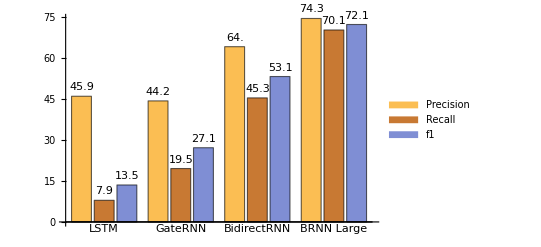

```mathematica
BarChart[{{45.9,7.9,13.5},{44.2,19.5,27.1},{64.0,45.3,53.1},{74.3,70.1,72.1}},ChartLabels->{{"LSTM","GateRNN","BidirectRNN","BRNN Large"},{"","",""}},LabelingFunction->Above,ChartLegends->{"Precision","Recall","f1"}]
```

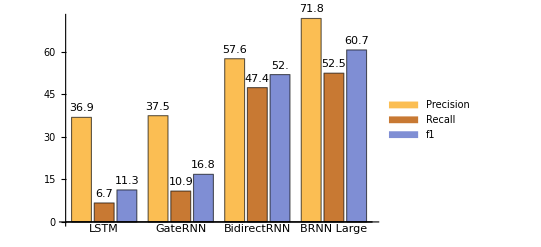

```mathematica
BarChart[{{36.9,6.7,11.3},{37.5,10.9,16.8},{57.6,47.4,52.0},{71.8,52.5,60.7}},ChartLabels->{{"LSTM","GateRNN","BidirectRNN","BRNN Large"},{"","",""}},LabelingFunction->Above,ChartLegends->{"Precision","Recall","f1"}]
```